Quadrupole Trap: using the Anti-Helmholtz coil configuration. The 3D field calculation is obtained from a series expansion of 1/|r-r’|^3 in the (elliptic integral). Nice derivation can be found here: http://publish.illinois.edu/davidchen/files/2012/10/Anti-Helmholtz-magnetic-trap.pdf

Assuming constant current, we can use Biot-Savart’s Law. From there, continue...

```mathematica
B3D[x_,y_,z_] := {x, y, -2*z};
```

```mathematica
VectorPlot3D[B3D[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
B2D[x_,z_]:={x,-2z};
```

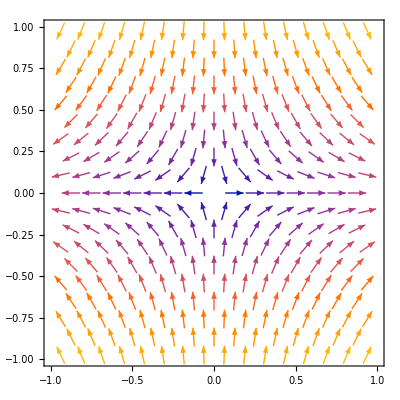

```mathematica
VectorPlot[B2D[x,z],{x,-1,1},{z,-1,1}]
```

```mathematica
NormB3D[x_,y_,z_]:=Norm[B3D[x,y,z]];
```

```mathematica
NormB2D[x_,z_]:=Norm[B2D[x,z]];
```

```mathematica
DensityPlot3D[NormB3D[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

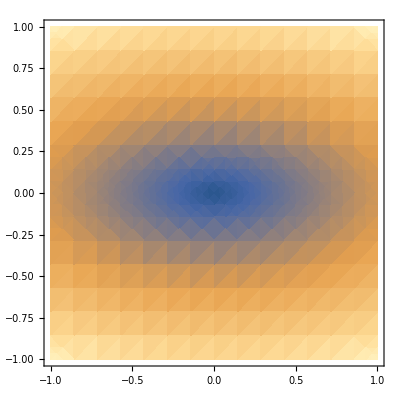

```mathematica
DensityPlot[NormB2D[x,z],{x,-1,1},{z,-1,1}]
```

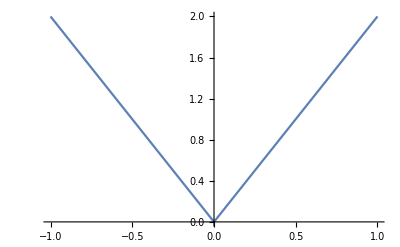

```mathematica
Plot[NormB3D[0,0,z],{z,-1,1}]
```

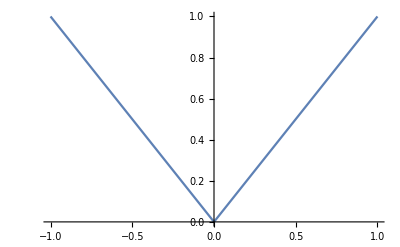

```mathematica
Plot[NormB3D[0,y,0],{y,-1,1}]
```

TOP trap: modifying the quadrupole trap inconvenience by removing the zero point magnetic field. The additional field is an XY-rotating bias field given by

```mathematica
BTime[x_,y_,z_,t_,Omega_] := {B*Cos[Omega*t], B*Sin[Omega*t], 0};
```

```mathematica
BTotal[x_,y_,z_,t_,Omega_]:=A*B3D[x,y,z]+BTime[x,y,z,t,Omega];
```

```mathematica
Norm[BTotal[x,y,z,t,Omega]]
```

√(4 Abs[A z]^2+Abs[A x+B Cos[Omega t]]^2+Abs[A y+B Sin[Omega t]]^2)

After some approximations (r =\sqrt{x^2 + y^2 + z^2} <<  R), the time-averaged magnetic field strength is

```mathematica
B=1;A=2;
```

```mathematica
BTAvg[x_,y_,z_]:=B+(A^2/(4*B))*(x^2+y^2+8*z^2);
```

```mathematica
DensityPlot3D[BTAvg[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

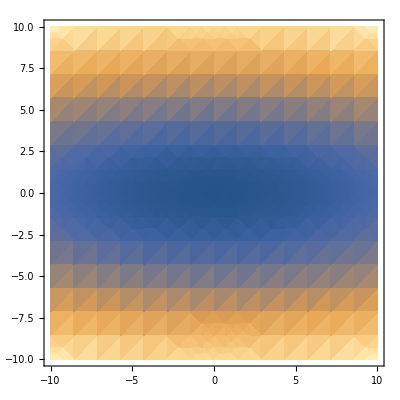

```mathematica
DensityPlot[BTAvg[x,0,z],{x,-10,10},{z,-10,10}]
```

Notice that we now have an effective anisotropic harmonic potential. At the origin, the magnetic field is now B.

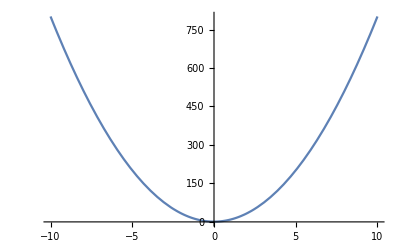

```mathematica
Plot[BTAvg[0,0,z],{z,-10,10}]
```

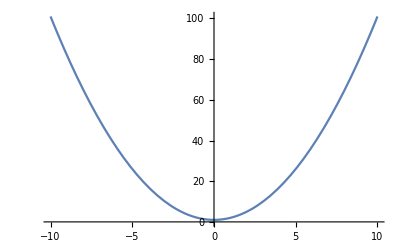

```mathematica
Plot[BTAvg[x,0,0],{x,-10,10}]
```

```mathematica
Plot[BTAvg[0,y,0],{y,-10,10}]
```

-Graphics-

How to use the field strength curvature to calculate \omega_x, \omega_y, \omega_z (trapping frequencies which atoms see)...

C^2*x^2/(4*B) = Bfield = -E/mu=-(m*omega^2*x^2)/(2*mu) ---> \omega_x = \sqrt{-mu*C^2/2mB}

8*C^2*z^2/(4*B) = Bfield = -E/mu=-(m*omega^2*z^2)/(2*mu) ---> \omega_z = \sqrt{-4mu*C^2/mB}

Finally we have the Ioffe-Pritchard trap. See source for the configuration.

```mathematica
a=1;b=1.2;
```

```mathematica
C1=-a^2/(a^2+b^2)^(3/2);C3=a^2*(a^2-4*b^2)/(2*(a^2+b^2)^(7/2));
```

```mathematica
BIP[x_,y_,z_]:={3*C3*z*x,3*C3*z*y,-(C1-(3/2)*C3*(x^2+y^2-2*z^2))};
```

```mathematica
VectorPlot3D[BIP[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
NormBIP[x_,y_,z_]:=Norm[BIP[x,y,z]]
```

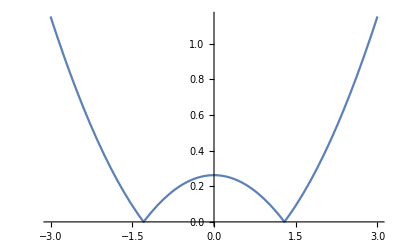

```mathematica
Plot[NormBIP[x,0,0],{x,-3,3}]
```

```mathematica
Plot[NormBIP[0,y,0],{y,-3,3}]
```

-Graphics-

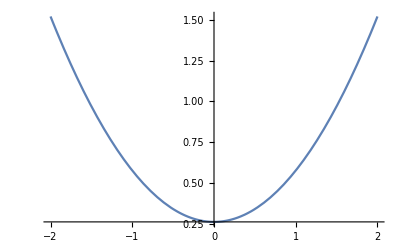

```mathematica
Plot[NormBIP[0,0,z],{z,-2,2}]
```

```mathematica
DensityPlot3D[NormBIP[x,y,z],{x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

Explicit Calculations:

```mathematica
l = {a*Cos[theta],a*Sin[theta], d};
```

```mathematica
Norm[l]//Simplify
```

√(Abs[d]^2+Abs[a Cos[theta]]^2+Abs[a Sin[theta]]^2)

```mathematica
dl = {-a*Sin[theta], a*Cos[theta],0};
```

```mathematica
r = {x,y,z};
```

```mathematica
r-l
```

{x-a Cos[theta],y-a Sin[theta],-d+z}

```mathematica
Cross[dl,(r-l)]/Norm[l]^3//Simplify
```

{-(a (d-z) Cos[theta])/((Abs[d]^2+Abs[a Cos[theta]]^2+Abs[a Sin[theta]]^2)^(3/2)),-(a (d-z) Sin[theta])/((Abs[d]^2+Abs[a Cos[theta]]^2+Abs[a Sin[theta]]^2)^(3/2)),(a (a-x Cos[theta]-y Sin[theta]))/((Abs[d]^2+Abs[a Cos[theta]]^2+Abs[a Sin[theta]]^2)^(3/2))}

```mathematica
A=(mu0*current/(4*Pi))*(1/(a^2+d^2)^(3/2))*Integrate[Cross[dl,(r-l)],{theta,0,2*Pi}]
```

{0,0,(a^2 current mu0)/(2 (a^2+d^2)^(3/2))}

```mathematica
Dot[r,l]
```

d z+a x Cos[theta]+a y Sin[theta]

```mathematica
B=(3*mu0*current/(4*Pi))*(1/(a^2+d^2)^(5/2))Integrate[Cross[dl, r-l]*Dot[r,l],{theta,0,2*Pi}]//Simplify
```

{-(3 a^2 current mu0 x (d-z))/(4 (a^2+d^2)^(5/2)),-(3 a^2 current mu0 y (d-z))/(4 (a^2+d^2)^(5/2)),-(3 a^2 current mu0 (x^2+y^2-2 d z))/(4 (a^2+d^2)^(5/2))}

Now remove all nonlinear terms:

```mathematica
BB=A+3*{-(a^2 current mu0 x (d))/(4 (a^2+d^2)^(5/2)),-(a^2 current mu0 y (d))/(4 (a^2+d^2)^(5/2)),-(a^2 current mu0 (-2 d z))/(4 (a^2+d^2)^(5/2))}//Simplify
```

{-(3 a^2 current d mu0 x)/(4 (a^2+d^2)^(5/2)),-(3 a^2 current d mu0 y)/(4 (a^2+d^2)^(5/2)),(a^2 current mu0 (a^2+d (d+3 z)))/(2 (a^2+d^2)^(5/2))}

Now do I ---> -I and a ---> -a and find the total field:

```mathematica
BB+{-(3 a^2 current d mu0 x)/(4 (a^2+d^2)^(5/2)),-(3 a^2 current d mu0 y)/(4 (a^2+d^2)^(5/2)),-(a^2 current mu0 (a^2-d (-d+3z)))/(2 (a^2+d^2)^(5/2))}//Simplify
```

{-(3 a^2 current d mu0 x)/(2 (a^2+d^2)^(5/2)),-(3 a^2 current d mu0 y)/(2 (a^2+d^2)^(5/2)),(3 a^2 current d mu0 z)/((a^2+d^2)^(5/2))}

```mathematica
Mag[x_,y_,z_,t_]:=B0*{x,y,-2z}+Brot*{Cos[ω*t], Sin[ω*t],0}
```

```mathematica
Norm[Mag[x,y,z,t]]
```

√(4 Abs[B0 z]^2+Abs[B0 x+Brot Cos[t ω]]^2+Abs[B0 y+Brot Sin[t ω]]^2)

```mathematica
Series[(1+e)^(-3/2),{e,0,5}]
```

1-(3 e)/2+(15 e^2)/8-(35 e^3)/16+(315 e^4)/128-(693 e^5)/256+O[e]^6

```mathematica
B0=(mu0*II/(4*Pi*Norm[l]^3))Integrate[Cross[dl,r-l],{theta,0,2Pi}]//Simplify
```

{0,0,(a^2 II mu0)/(2 (Abs[d]^2+Abs[a Cos[theta]]^2+Abs[a Sin[theta]]^2)^(3/2))}

```mathematica
B1=(3*mu0*II/(4*Pi))Integrate[Cross[dl,r-l]*Dot[r,l],{theta,0,2Pi}]//Simplify
```

{-3/4 a^2 II mu0 x (d-z),-3/4 a^2 II mu0 y (d-z),-3/4 a^2 II mu0 (x^2+y^2-2 d z)}

```mathematica
B1 = B1/Norm[l]^5
```

{-(3 a^2 II mu0 x (d-z))/(4 (Abs[d]^2+Abs[a Cos[theta]]^2+Abs[a Sin[theta]]^2)^(5/2)),-(3 a^2 II mu0 y (d-z))/(4 (Abs[d]^2+Abs[a Cos[theta]]^2+Abs[a Sin[theta]]^2)^(5/2)),-(3 a^2 II mu0 (x^2+y^2-2 d z))/(4 (Abs[d]^2+Abs[a Cos[theta]]^2+Abs[a Sin[theta]]^2)^(5/2))}

```mathematica
B2=(15*mu0*II/(8*Pi))Integrate[Cross[dl,r-l]*Dot[r,l]*Dot[r,l],{theta,0,2Pi}]//Simplify
```

{-15/4 a^2 d II mu0 x (d-z) z,-15/4 a^2 d II mu0 y (d-z) z,15/8 a^2 II mu0 (a^2 (x^2+y^2)+2 d z (-x^2-y^2+d z))}